```mathematica
Table[i,{i,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
$ProcessorCount
```

2

```mathematica
$ConfiguredKernels
```

{«2 local kernels»,«4 kernels on hartree.cmth.ph.ic.ac.uk»}

```mathematica
LaunchKernels[8]
```

{KernelObject[7,local],KernelObject[8,local],KernelObject[9,local],KernelObject[10,local],KernelObject[11,local],KernelObject[12,local],KernelObject[13,local],KernelObject[14,local]}

```mathematica
Kernels[]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local]}

```mathematica
Total[Flatten[Table[Table[Table[i^j^k,{i,1,10}],{j,1,5}],{k,1,9}]]]//Timing
```

{0.170907,10000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000019528738126368315446315382314463193608747846334630622255520069654669887337521080266337483744391632223747285502951854328154414307184991}
 |  |  |  |

```mathematica
Total[Flatten[Parallelize[Table[Table[Table[i^j^k,{i,1,10}],{j,1,5}],{k,1,9}]]]]//Timing
```

{2.0016,10000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000019528738126368315446315382314463193608747846334630622255520069654669887337521080266337483744391632223747285502951854328154414307184991}
 |  |  |  |

```mathematica
TableForm[ParallelEvaluate[{$KernelID,$MachineName,$SystemID,$VersionNumber,$ProcessID,TimeUsed[],MaxMemoryUsed[],"ProcessPriority"/.SystemOptions["ProcessPriority"]}],TableHeadings->{None,{"ID","host","OS","Version","Process","CPU Time","Memory","Priority"}},TableDepth->2]
```

```mathematica
$KernelCount
```

0

```mathematica
CloseKernels[10]
```

Kernels::noid: No parallel kernel with ID 10 found.

$Failed

```mathematica
$KernelCount
AbortKernels[]
```

6

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local]}

```mathematica
$CommandLine
```

{/Applications/Mathematica 2.app/Contents/MacOS/WolframKernel,-wstp,-mathlink,-linkprotocol,SharedMemory,-linkconnect,-linkname,vse5r_shm}

```mathematica
(*Standard coefficients - ZrC mass + Boltzmann*)
m={12.0107,91.224,1};kB=1000*8.617332478*10^−5;K2meV=1000*8.617332478*10^−5;
(*Data in*)
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/allvols"];
filesC={"C_4575","C_4600","C_4625","C_46583","C_4685_760","C_4730_1900","C_4759_2500","C_4801_3200","C_4850_3805","C_4575_110","C_4600_110","C_4625_110","C_46583_110","C_4685_760_110","C_4730_1900_110","C_4759_2500_110","C_4801_3200_110","C_4850_3805_110","C_4575_111","C_4600_111","C_4625_111","C_46583_111","C_4685_760_111","C_4730_1900_111","C_4759_2500_111","C_4801_3200_111","C_4850_3805_111"};
filesZr={"Zr_4575","Zr_4600","Zr_4625","Zr_46583","Zr_4685_760","Zr_4730_1900","Zr_4759_2500","Zr_4801_3200","Zr_4850_3805","Zr_4575_110","Zr_4600_110","Zr_4625_110","Zr_46583_110","Zr_4685_760_110","Zr_4730_1900_110","Zr_4759_2500_110","Zr_4801_3200_110","Zr_4850_3805_110","Zr_4575_111","Zr_4600_111","Zr_4625_111","Zr_46583_111","Zr_4685_760_111","Zr_4730_1900_111","Zr_4759_2500_111","zr_4801_3200_111","Zr_4850_3805_111"};
filesCh={"1.harm.C_4575","1.harm.C_4600","1.harm.C_4625","1.harm.C_46583","1.harm.C_4685_760","1.harm.C_4730_1900","1.harm.C_4759_2500","1.harm.C_4801_3200","1.harm.C_4850_3805","1.harm.C_4575_110","1.harm.C_4600_110","1.harm.C_4625_110","1.harm.C_46583_110","1.harm.C_4685_760_110","1.harm.C_4730_1900_110","1.harm.C_4759_2500_110","1.harm.C_4801_3200_110","1.harm.C_4850_3805_110","1.harm.C_4575_111","1.harm.C_4600_111","1.harm.C_4625_111","1.harm.C_46583_111","1.harm.C_4685_760_111","1.harm.C_4730_1900_111","1.harm.C_4759_2500_111","1.harm.C_4801_3200_111","1.harm.C_4850_3805_111"};
filesZrh={"1.harm.Zr_4575","1.harm.Zr_4600","1.harm.Zr_4625","1.harm.Zr_46583","1.harm.Zr_4685_760","1.harm.Zr_4730_1900","1.harm.Zr_4759_2500","1.harm.Zr_4801_3200","1.harm.Zr_4850_3805","1.harm.Zr_4575_110","1.harm.Zr_4600_110","1.harm.Zr_4625_110","1.harm.Zr_46583_110","1.harm.Zr_4685_760_110","1.harm.Zr_4730_1900_110","1.harm.Zr_4759_2500_110","1.harm.Zr_4801_3200_110","1.harm.Zr_4850_3805_110","1.harm.Zr_4575_111","1.harm.Zr_4600_111","1.harm.Zr_4625_111","1.harm.Zr_46583_111","1.harm.Zr_4685_760_111","1.harm.Zr_4730_1900_111","1.harm.Zr_4759_2500_111","1.harm.Zr_4801_3200_111","1.harm.Zr_4850_3805_111"};
Cdata=Table[ReadList[filesC[[i]],{Number, Number}],{i,1,27}];
Zrdata=Table[ReadList[filesZr[[i]],{Number, Number}],{i,1,27}];
hCdata=Table[ReadList[filesCh[[i]],{Number, Number}],{i,1,27}];
hZrdata=Table[ReadList[filesZrh[[i]],{Number, Number}],{i,1,27}];
```

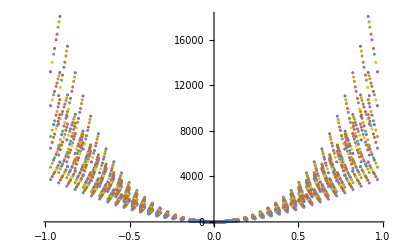

```mathematica
Show[ListPlot@Cdata,ListPlot@Zrdata,PlotRange->All]
```

```mathematica
Define and fit potentials;
(* Potentials are defined like: V[element,order polynomial, variable] *)
(*Carbon*)
V[1,2,x_]:=Table[Fit[hCdata[[i]],{x^2},x],{i,1,15}]
V[1,4,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4},x],{i,1,15}]
V[1,6,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6},x],{i,1,15}]
V[1,8,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8},x],{i,1,15}]
V[1,10,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10},x],{i,1,15}]
V[1,12,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,15}]
(*Zirconium*)
V[2,2,x_]:=Table[Fit[hZrdata[[i]],{x^2},x],{i,1,15}]
V[2,4,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4},x],{i,1,15}]
V[2,6,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6},x],{i,1,15}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8},x],{i,1,15}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10},x],{i,1,15}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,15}]
```

```mathematica
rule1={α->(x/Sqrt[1]),α->(y/Sqrt[1]),α->(z/Sqrt[1])}
rule2={β->((x+y)),β->((x-y)),β->((y+z)),β->((y-z)),β->((z+x)),β->((z-x))}
rule3={γ->((x+y+z)),γ->((x+y-z)),γ->((x-y+z)),γ->((x-y-z))}
```

{α→x,α→y,α→z}

{β→x+y,β→x-y,β→y+z,β→y-z,β→x+z,β→-x+z}

{γ→x+y+z,γ→x+y-z,γ→x-y+z,γ→x-y-z}

```mathematica
U1[e_,o_,x_,y_,z_]:=(3/3)*Sum[V[e,o,α][[1]]/.rule1[[i]],{i,1,3}]//Simplify
U2[e_,o_,x_,y_,z_]:=(3/12)*Sum[V[e,o,β][[6]]/.rule2[[i]],{i,1,6}]//Simplify
U3[e_,o_,x_,y_,z_]:=(3/12)*Sum[V[e,o,γ][[11]]/.rule3[[i]],{i,1,4}]//Simplify
UUU[e_,o_,x_,y_,z_]:=U1[e,o,x,y,z]+(U2[e,o,x,y,z]-U1[e,o,x,y,z])+(U3[e,o,x,y,z]-(U1[e,o,x,y,z]+(U2[e,o,x,y,z]-U1[e,o,x,y,z])))
```

```mathematica
contourOptions={AxesLabel->{"x (Å)","z (Å)"},ImageSize->300};
cHar=Table[With[{B=0.25*i},ContourPlot[UUU[1,2,x,y,z]/.y->0,{x,-B,B},{z,-B,B},PlotLegends->Automatic,Evaluate@contourOptions]],{i,1,4}];
cAnh=Table[With[{B=0.25*i},ContourPlot[UUU[1,6,x,y,z]/.y->0,{x,-B,B},{z,-B,B},PlotLegends->Automatic,Evaluate@contourOptions]],{i,1,4}];
zHar=Table[With[{B=0.25*i},ContourPlot[UUU[2,2,x,y,z]/.y->0,{x,-B,B},{z,-B,B},PlotLegends->Automatic,Evaluate@contourOptions]],{i,1,4}];
zAnh=Table[With[{B=0.25*i},ContourPlot[UUU[2,6,x,y,z]/.y->0,{x,-B,B},{z,-B,B},PlotLegends->Automatic,Evaluate@contourOptions]],{i,1,4}];
```

```mathematica
GraphicsGrid[{{cHar[[4]],cAnh[[4]]},{zHar[[4]],zAnh[[4]]}},ImageSize->1000]
```

-Graphics-

```mathematica
SUUU[e_,o_,R_,θ_,ϕ_]:=TransformedField["Cartesian"->"Spherical",UUU[e,o,x,y,z],{x,y,z}->{R,θ,ϕ}]
ℒanhzS=-(1/(2m[[2]]))*Laplacian[u[R,θ,ϕ],{R,θ,ϕ},"Spherical"]+SUUU[2,6,R,θ,ϕ]*u[R,θ,ϕ]
solverOptions={Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0008}}},"Eigensystem"->{"Arnoldi",MaxIterations->10000}}};
```

-2833.44 (-3.64632 R^2 Cos[θ]^2-1.6701 R^4 Cos[θ]^4+1. R^6 Cos[θ]^6-3.64632 R^2 Cos[ϕ]^2 Sin[θ]^2-10.0206 R^4 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2+15. R^6 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2-1.6701 R^4 Cos[ϕ]^4 Sin[θ]^4+15. R^6 Cos[θ]^2 Cos[ϕ]^4 Sin[θ]^4+1. R^6 Cos[ϕ]^6 Sin[θ]^6-3.64632 R^2 Sin[θ]^2 Sin[ϕ]^2-10.0206 R^4 Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2+15. R^6 Cos[θ]^4 Sin[θ]^2 Sin[ϕ]^2-10.0206 R^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2+90. R^6 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2+15. R^6 Cos[ϕ]^4 Sin[θ]^6 Sin[ϕ]^2-1.6701 R^4 Sin[θ]^4 Sin[ϕ]^4+15. R^6 Cos[θ]^2 Sin[θ]^4 Sin[ϕ]^4+15. R^6 Cos[ϕ]^2 Sin[θ]^6 Sin[ϕ]^4+1. R^6 Sin[θ]^6 Sin[ϕ]^6) u[R,θ,ϕ]-0.00548101 (((u^(0,2,0)[R,θ,ϕ])/R+u^(1,0,0)[R,θ,ϕ])/R+(Csc[θ] ((Csc[θ] u^(0,0,2)[R,θ,ϕ])/R+(Cos[θ] u^(0,1,0)[R,θ,ϕ])/R+Sin[θ] u^(1,0,0)[R,θ,ϕ]))/R+u^(2,0,0)[R,θ,ϕ])

```mathematica
Carbon and zirconium - calculate eigenvalues and vectors;
(*Find the first x eigenvalues and eigenvectors*)
Neigenvalues=20;
B=1;H=2000;
ℒharcS=-(1/(2m[[1]]))*Laplacian[u[R,θ,ϕ],{R,θ,ϕ},"Spherical"]+SUUU[1,2,R,θ,ϕ]*u[R,θ,ϕ];
ℒharzS=-(1/(2m[[2]]))*Laplacian[u[R,θ,ϕ],{R,θ,ϕ},"Spherical"]+SUUU[2,2,R,θ,ϕ]*u[R,θ,ϕ];
ℒanhcS=-(1/(2m[[1]]))*Laplacian[u[R,θ,ϕ],{R,θ,ϕ},"Spherical"]+SUUU[1,6,R,θ,ϕ]*u[R,θ,ϕ];
ℒanhzS=-(1/(2m[[2]]))*Laplacian[u[R,θ,ϕ],{R,θ,ϕ},"Spherical"]+SUUU[2,6,R,θ,ϕ]*u[R,θ,ϕ];
solverOptions={Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0008}}},"Eigensystem"->{"Arnoldi",MaxIterations->10000}}};
```

```mathematica
harcS=NDEigensystem[ℒharcS,u[R,θ,ϕ],{R,0,B/3},{θ,0,Pi},{ϕ,0,2Pi},Neigenvalues,Evaluate@solverOptions]//Timing;
harzS=NDEigensystem[ℒharcS,u[R,θ,ϕ],{R,0,B/3},{θ,0,Pi},{ϕ,0,2Pi},Neigenvalues,Evaluate@solverOptions]//Timing;
```

$Aborted

```mathematica
harcS[[2]]
harzS[[1]]
```

NDEigensystem[(7325.14 R^2 Cos[θ]^2+7325.14 R^2 Cos[ϕ]^2 Sin[θ]^2+7325.14 R^2 Sin[θ]^2 Sin[ϕ]^2) u[R,θ,ϕ]-0.0416295 (((u^(0,2,0)[R,θ,ϕ])/R+u^(1,0,0)[R,θ,ϕ])/R+(Csc[θ] ((Csc[θ] u^(0,0,2)[R,θ,ϕ])/R+(Cos[θ] u^(0,1,0)[R,θ,ϕ])/R+Sin[θ] u^(1,0,0)[R,θ,ϕ]))/R+u^(2,0,0)[R,θ,ϕ]),u[R,θ,ϕ],{R,0,B/3},{θ,0,π},{ϕ,0,2 π},20,{Method→{SpatialDiscretization→{FiniteElement,{MeshOptions→{MaxCellMeasure→0.0008}}},Eigensystem→{Arnoldi,MaxIterations→10000}}}]

0.00028

```mathematica
hanhcS=NDEigensystem[ℒharcS,u[R,θ,ϕ],{R,0,B/3},{θ,0,Pi},{ϕ,0,2Pi},Neigenvalues,Evaluate@solverOptions]//Timing;
hanhzS=NDEigensystem[ℒharcS,u[R,θ,ϕ],{R,0,B/3},{θ,0,Pi},{ϕ,0,2Pi},Neigenvalues,Evaluate@solverOptions]//Timing;
```

```mathematica
hanhcS[[1]]
hanhzS[[1]]
```

0.000339

0.000281

```mathematica
hanhcS
```

{0.000339,NDEigensystem[(7325.14 R^2 Cos[θ]^2+7325.14 R^2 Cos[ϕ]^2 Sin[θ]^2+7325.14 R^2 Sin[θ]^2 Sin[ϕ]^2) u[R,θ,ϕ]-0.0416295 (((u^(0,2,0)[R,θ,ϕ])/R+u^(1,0,0)[R,θ,ϕ])/R+(Csc[θ] ((Csc[θ] u^(0,0,2)[R,θ,ϕ])/R+(Cos[θ] u^(0,1,0)[R,θ,ϕ])/R+Sin[θ] u^(1,0,0)[R,θ,ϕ]))/R+u^(2,0,0)[R,θ,ϕ]),u[R,θ,ϕ],{R,0,B/3},{θ,0,π},{ϕ,0,2 π},4,{Method→{SpatialDiscretization→{FiniteElement,{MeshOptions→{MaxCellMeasure→0.0008}}},Eigensystem→{Arnoldi,MaxIterations→10000}}}]}